```mathematica
Quit[]
```

## Graphics

```mathematica
ImportGC[x_]:=ReadList[StringToStream[x],{Number,Number}];
```

```mathematica
<<Graphics`Graphics`;
Off[General::"spell",General::"spell1"];Off[NumberForm::sigz];
```

Get::noopen: Cannot open "Graphics`Graphics`".

```mathematica
$TextStyle={FontFamily->"Times",FontSize->11};
```

```mathematica
cfgreen=Function[z, Which[z<0.99,Hue[0.25,1- Sqrt[z],1],z>0.99,RGBColor[1,1,1]]];
```

```mathematica
cf1=Function[z,RGBColor[1,1,1-z]];
cf2=Function[z,Which[z==1,RGBColor[1,1,0],z<1/2,
			RGBColor[1,1,1-z/2],z>1/2,RGBColor[1,1,0.6]]];
cf3=Function[z,RGBColor[1,1,1-Sqrt[z]]];
cf4=Function[z,RGBColor[1,1,√z]];
cfRG=Function[z,Which[z<0.49,Hue[0.4,Sqrt[1-2z],1],z>0.51,Hue[0, Sqrt[2 z-1],1],True,GrayLevel[1]]];
```

```mathematica
LogLogTicks[a_,b_]:={LogLogTicks[a]⟦1⟧,LogLogTicks[b]⟦2⟧,LogLogTicks[a]⟦3⟧,LogLogTicks[b]⟦4⟧};
```

#### dettaglio: 1,3,10,30

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-60,20}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1||m==3,{Log[10.,m*10^n],If[m==1,DisplayForm[m*SuperscriptBox[10,n]],
						DisplayForm[SuperscriptBox[" ",3]]]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-50,20}],1];
LinLogTicks[dettaglio]={Automatic,llab,Automatic,ltick};
LogLinTicks[dettaglio]={llab,Automatic,ltick,Automatic};
LogLogTicks[dettaglio]={llab,llab,ltick,ltick};
```

#### dettaglio1: 1,3,10,30

```mathematica
Clear[n,m];llab=Table[tick[n,m],{m,1,9},{n,-10,10}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1||m==3,{Log[10.,m*10^n],If[n<0,N[m 10^n],m*10^n]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-20,20}],1];
LinLogTicks[dettaglio1]={Automatic,llab,Automatic,ltick};
LogLinTicks[dettaglio1]={llab,Automatic,ltick,Automatic};
LogLogTicks[dettaglio1]={llab,llab,ltick,ltick};
```

#### normale: 10^i

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-60,60}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],DisplayForm[m*SuperscriptBox[10,n]]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-60,40}],1];
LinLogTicks[normale]={Automatic,llab,Automatic,ltick};
LogLinTicks[normale]={llab,Automatic,ltick,Automatic};
LogLogTicks[normale]={llab,llab,ltick,ltick};
```

#### normaleN 0.1,1,10,100,1000,....

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-4,4}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],If[n<0,N[10^n],10^n]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-4,4}],1];
LinLogTicks[normaleN]={Automatic,llab,Automatic,ltick};
LogLinTicks[normaleN]={llab,Automatic,ltick,Automatic};
LogLogTicks[normaleN]={llab,llab,ltick,ltick};
```

#### normaleE: 0.1,1,10,100,10^3,....

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-20,20}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],If[-3<n<4,If[n<0,N[10^n],10^n],DisplayForm[m*SuperscriptBox[10,n]]]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-4,4}],1];
LinLogTicks[normaleE]={Automatic,llab,Automatic,ltick};
LogLinTicks[normaleE]={llab,Automatic,ltick,Automatic};
LogLogTicks[normaleE]={llab,llab,ltick,ltick};
```

#### normalee: 0.1,1,10,10^2,10^3,....

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-50,50}];llab=Flatten[llab]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],If[-1<n<2,If[n<0,N[10^n],10^n],DisplayForm[m*SuperscriptBox[10,n]]]},{Log[10.,m*10^n],""}];
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-50,50}],1];
LinLogTicks[normalee]={Automatic,llab,Automatic,ltick};
LogLinTicks[normalee]={llab,Automatic,ltick,Automatic};
LogLogTicks[normalee]={llab,llab,ltick,ltick};
```

#### solopari: 10^-2, 10^0, 10^2

```mathematica
llab2=Table[If[Mod[n,2]==0,{n,DisplayForm[SuperscriptBox[10,n]]},{n,""}],{n,-50,30}]/.DisplayForm[SuperscriptBox[10,0]]->1;
ltick2=Table[{n,""},{n,-50,30}];
LinLogTicks[solopari]={Automatic,llab2,Automatic,ltick2};
LogLinTicks[solopari]={llab2,Automatic,ltick2,Automatic};
LogLogTicks[solopari]={llab2,llab2,ltick2,ltick2};
```

#### solo5

```mathematica
llab2=Table[If[Mod[n,5]==0,{n,DisplayForm[SuperscriptBox[10,n]]},{n,""}],{n,-30,30}];
ltick2=Table[{n,""},{n,-30,30}];
LinLogTicks[solo5]={Automatic,llab2,Automatic,ltick2};
LogLinTicks[solo5]={llab2,Automatic,ltick2,Automatic};
LogLogTicks[solo5]={llab2,llab2,ltick2,ltick2};
```

#### superdettaglio: 1,2,3,4,5,6,7,8,9,10,20,30...

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-20,20}];llab=Flatten[llab]/.tick[n_,m_]->{Log[10.,y=m*10^n;If[y<1,N[y],y]],If[m==1,DisplayForm[m*SuperscriptBox[10,n]],
						DisplayForm[SuperscriptBox[" ",m]]]};
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-20,20}],1];
LinLogTicks[superdettaglio]={Automatic,llab,Automatic,ltick};
LogLinTicks[superdettaglio]={llab,Automatic,ltick,Automatic};
LogLogTicks[superdettaglio]={llab,llab,ltick,ltick};
```

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-3,3}];llab=Flatten[llab]/.tick[n_,m_]->{Log[10.,m*10^n],DisplayForm[m 10^n]};
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-20,20}],1];
LinLogTicks[superdettaglio2]={Automatic,llab,Automatic,ltick};
LogLinTicks[superdettaglio2]={llab,Automatic,ltick,Automatic};
LogLogTicks[superdettaglio2]={llab,llab,ltick,ltick};
```

```mathematica
llab=Table[tick[n,m],{m,1,9},{n,-20,20}];llab=Flatten[llab]/.tick[n_,m_]->{Log[10.,m*10^n],If[m==1||m==2||m==3||m==4||m==6||m==8,DisplayForm[If[n>-1,m 10^n,N[m 10^n]]],
				""]};
ltick=Flatten[Table[{Log[10.,m*10^n],""},{m,1,9},{n,-20,20}],1];
LinLogTicks[superdettaglio3]={Automatic,llab,Automatic,ltick};
LogLinTicks[superdettaglio3]={llab,Automatic,ltick,Automatic};
LogLogTicks[superdettaglio3]={llab,llab,ltick,ltick};
```

```mathematica
(*fa i ticks per dx e sx*)
llabLUMI=Table[tick[n,m],{m,1,9},{n,-50,50}];llabLUMI=Flatten[llabLUMI]/.tick[n_,m_]->If[m==1,{Log[10.,m*10^n],If[-1<n<2,If[n<0,N[10^n],10^n],DisplayForm[m*SuperscriptBox[10,n]]]},{Log[10.,m*10^n],""}];
myticks={Automatic,llabLUMI,None,llabLUMI};
```

## Main Functions

#### Inputs and constants

```mathematica
MW=80.3;
δwino=0.166;
sWq=0.2336;
cWq=1-sWq;
α2=0.03347006972484925;
α=α2*sWq;
MZ=MW/Sqrt[cWq];
rescalefromGEV=1.1673297487162315*^-17;
```

#### Main functions ‘WINO’

```mathematica
WINO[M_,v_,δ_,v1_,v3_,v5_,x0_]:=Module[{χ,χ00,χ01,χ10,χ11,r,z,SOL1,SOL2,VSU2,VDARK,S1,S2,S3,zmin,zmax},

zmin=0.001v/x0;
zmax=1;

(*DIFFERENTIAL EQUATIONS AND NUMERICAL SOLUTIONS*)
χ[z_]:={χ10[z],χ00[z]};
VSU2[r_]:=-α2/r({{cWq Exp[-MZ r]+sWq, Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});
VDARK[r_]:=-v1*M(1-UnitStep[r-1/(x0 M)])1/3({{2, √2}, {√2, 1}})-v5*M(1-UnitStep[r-1/(x0 M)])1/3({{1, -√2}, {-√2, 2}});
(*VSU2[r_]:=-α2/r({{Exp[-MW r], Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});*)
SOL1=NDSolve[{-χ''[z]+M/(M v)^2(({{2δ, 0}, {0, 0}})+VSU2[z/(M v)]).χ[z]==χ[z],
χ[zmin]=={0,0},
χ00'[zmax]-I χ00[zmax]==(√(4π))/(M v)Exp[-I zmax],χ10[zmax]==0},
(*χ'[zmax]-I DiagonalMatrix[{Sqrt[1-(2δ)/(M v^2)],1}].χ[zmax]==(√(4π))/(M v){0,Exp[-I zmax]}  },*)
{χ00,χ10},{z,zmin,zmax}];

SOL2=NDSolve[{-χ''[z]+M/(M v)^2(({{2δ, 0}, {0, 0}})+VSU2[z/(M v)]+VDARK[z/(M v)]).χ[z]==χ[z],
χ[zmin]=={0,0},
χ00'[zmax]-I χ00[zmax]==(√(4π))/(M v)Exp[-I zmax],χ10[zmax]==0},
{χ00,χ10},{z,zmin,zmax},AccuracyGoal->10,PrecisionGoal->10];

(*SOMMERFELD MATRIX*)
S1=((M v)/(√(4π))) χ'[zmin]/.SOL1[[1]];
S2=((M v)/(√(4π))) χ'[zmin]/.SOL2[[1]];
S3=((M v)/(√(4π))) χ'[v/x0]/.SOL2[[1]];

(*RETURN THE FOLLOWING QUANTITIES*)
{χ00/.SOL1[[1]],χ10/.SOL1[[1]],S1,S2,S3}
]
```

#### Main functions ‘DARK’

```mathematica
DARK[M_,v_,δ_,v1_,v3_,v5_,x0_]:=Module[{chibound,χ,χ00,χ10,r,z,SOL,VSU2,Sfactor,S00,VDARK,zmin,zmax,ai},

zmin=0.001 v/x0;
zmax=1;

(*DIFFERENTIAL EQUATIONS AND NUMERICAL SOLUTION*)
χ[z_]:={χ10[z],χ00[z]};
VSU2[r_]:=-α2/r({{cWq Exp[-MZ r]+sWq, Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});
(*VSU2[r_]:=-α2/r({{Exp[-MW r], Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});*)
VDARK[r_]:=-v1*M(1-UnitStep[r-1/(x0 M)])1/3({{2, √2}, {√2, 1}})-v5*M(1-UnitStep[r-1/(x0 M)])1/3({{1, -√2}, {-√2, 2}});
SOL=NDSolve[{-χ''[z]+M/(M v)^2(({{2δ, 0}, {0, 0}})+VSU2[z/(M v)]+VDARK[z/(M v)]).χ[z]==χ[z],
χ[zmin]=={0,0},
χ00'[zmax]-I χ00[zmax]==(√(4π))/(M v)Exp[-I zmax],χ10[zmax]==0 },
{χ00,χ10},{z,zmin,zmax},AccuracyGoal->10,PrecisionGoal->10];

(*SOMMERFELD MATRIX*)
Sfactor=((M v)/Sqrt[4π]){χ10'[zmin],χ00'[zmin]}/.SOL[[1]];

(*SCATTERING LENGTH*)

ai=-(ArcSin[(M v)/(√(4π))χ00[zmax]/.SOL[[1]]]-zmax)/(M v);


(*RETURN THE FOLLOWING QUANTITIES*)
{χ00/.SOL[[1]],χ10/.SOL[[1]],ai}
]
```

#### Main functions ‘DARKoverlap’

```mathematica
DARKoverlap[M_,v_,δ_,v1_,v3_,v5_,x0_,binding_]:=Module[{chibound,χ,sol10,χ10,χ00,r,z,SOL,VSU2,VDARK,zmin,zmax},
(*DIFFERENTIAL EQUATIONS AND NUMERICAL SOLUTION*)

zmin=0.001v/x0;
zmax=1;

χ[z_]:={χ10[z],χ00[z]};
VSU2[r_]:=-α2/r({{cWq Exp[-MZ r]+sWq, Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});
(*VSU2[r_]:=-α2/r({{Exp[-MW r], Exp[-MW r] √2}, {Exp[-MW r] √2, 0}});*)
VDARK[r_]:=-v1*M(1-UnitStep[r-1/(x0 M)])1/3({{2, √2}, {√2, 1}})-v5*M(1-UnitStep[r-1/(x0 M)])1/3({{1, -√2}, {-√2, 2}});
SOL=NDSolve[{-χ''[z]+M/(M v)^2(({{2δ, 0}, {0, 0}})+VSU2[z/(M v)]+VDARK[z/(M v)]).χ[z]==χ[z],
(*χ'[zmin]==1/zmin χ[zmin],*)

χ[zmin]=={0,0},
χ00'[zmax]-I χ00[zmax]==(√(4π))/(M v)Exp[-I zmax],χ10[zmax]==0},
(*χ'[zmax]-I DiagonalMatrix[{Sqrt[1-(2δ)/(M v^2)],1}].χ[zmax]==(√(4π))/(M v){0,Exp[-I zmax]}  },*)
{χ00,χ10},{z,zmin,zmax},AccuracyGoal->10,PrecisionGoal->10];

chibound[r_,V0_,B_,r0_]:=(√(2 √(M B)))/(√(1+r0 Sqrt[M B]))( Sin[√(M (V0-B))r]UnitStep[r0-r]+ ⅇ^(√(B M) r0) Sin[r0 √(M (-B+V0))] Exp[-√(M B)r]UnitStep[r-r0]);
sol10=χ10/.SOL[[1]];
Abs[NIntegrate[chibound[z/(M v),v3*M,binding*M,1/(x0 M)] sol10[z]/(M v),{z,zmin,(10 v)/Sqrt[binding]}]]^2
]
```

## Results

```mathematica
(*INPUTS for variuous channels*)
β=0.001;
δwino=.166;
masses=Table[1000+i*50,{i,1,100}];
x0=1;
```

```mathematica
eqB[B_,V0_,x0_]:=Abs[√B+√(V0-B) Cot[ √(V0-B)/x0]];
b1=0.1;
b3=b1/2;
b5=b1/18;
vpot1= v0/.FindRoot[eqB[b1,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot3=v0/.FindRoot[eqB[b3,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot5=v0/.FindRoot[eqB[b5,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
```

3.16113

2.94499

2.6198

```mathematica
SIGMAoverlap=Table[{masses[[i]],0.3894×10^(-27)*2.998×10^10((8 α2 sWq)(b3 masses[[i]])^(3))/masses[[i]]^2 DARKoverlap[masses[[i]],β,δwino,vpot1,vpot3,vpot5,x0,b3]},{i,1,Length[masses]}];
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 53.0641 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

```mathematica
Γbs=0.3894×10^(-27)*2.998×10^10({{(1-Sqrt[b3/b1]+1/2(1-Sqrt[b3/b5]))^2, -(1-Sqrt[b3/b1]+1/2(1-Sqrt[b3/b5]))(Sqrt[b3/b1]-Sqrt[b3/b5])/Sqrt[2]}, {-(1-Sqrt[b3/b1]+1/2(1-Sqrt[b3/b5]))(Sqrt[b3/b1]-Sqrt[b3/b5])/Sqrt[2], (Sqrt[b3/b1]-Sqrt[b3/b5])^2/2}});
SEW1=Table[{masses[[i]],WINO[masses[[i]],β,δwino,vpot1,vpot3,vpot5,x0][[3]]},{i,1,Length[masses]}];
SIGMAfactorized1=Table[{masses[[i]],2((2^7π α2 sWq)b3^(3/2))/(9masses[[i]]^2)Abs[Conjugate[SEW1[[i]][[2]]].Γbs.SEW1[[i]][[2]]]},{i,1,Length[masses]}];
SEW2=Table[{masses[[i]],WINO[masses[[i]],β,δwino,vpot1,vpot3,vpot5,x0][[4]]},{i,1,Length[masses]}];
SIGMAfactorized2=Table[{masses[[i]],2((2^7π α2 sWq)b3^(3/2))/(9masses[[i]]^2)Abs[Conjugate[SEW2[[i]][[2]]].Γbs.SEW2[[i]][[2]]]},{i,1,Length[masses]}];
SEW3=Table[{masses[[i]],WINO[masses[[i]],β,δwino,vpot1,vpot3,vpot5,x0][[5]]},{i,1,Length[masses]}];
SIGMAfactorized3=Table[{masses[[i]],2((2^7π α2 sWq)b3^(3/2))/(9masses[[i]]^2)Abs[Conjugate[SEW3[[i]][[2]]].Γbs.SEW3[[i]][[2]]]},{i,1,Length[masses]}];
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 53.0641 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 53.0641 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 53.0641 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

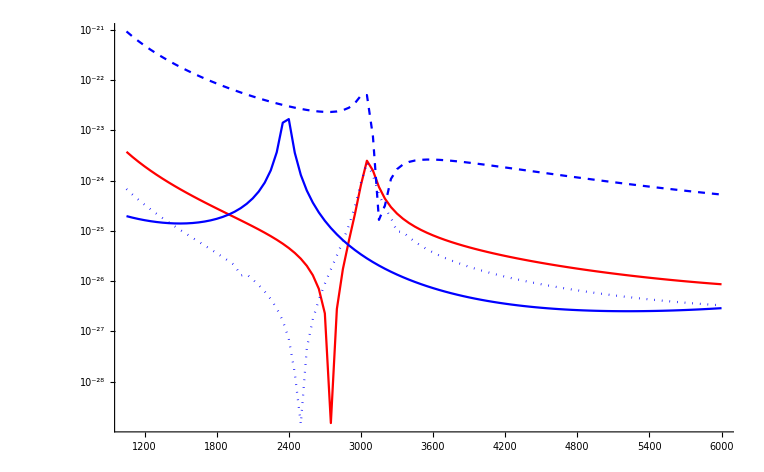

```mathematica
(*LogPlot[{Interpolation[SIGMAfactorized][m],Interpolation[SIGMAoverlap][m]},{m,1000,3500}]*)
Show[ListLogPlot[SIGMAoverlap,Joined->True,PlotStyle->Red],ListLogPlot[SIGMAfactorized1,Joined->True,PlotStyle->Blue],ListLogPlot[SIGMAfactorized2,Joined->True,PlotStyle->{Blue,Dashed}],ListLogPlot[SIGMAfactorized3,Joined->True,PlotStyle->{Blue,Dotted}],PlotRange->All]
```

```mathematica
SIGMAfactorized[[10,2]]
SIGMAoverlap[[10,2]]
```

Part::partd: Part specification SIGMAfactorized⟦10,2⟧ is longer than depth of object.

SIGMAfactorized⟦10,2⟧

6.69377×10^-25

## checks

```mathematica
(*INPUTS for variuous channels*)
β=0.001;
δwino= .166;
masses=Table[1000+i*50,{i,1,100}];
x0=10;
mdm=3000
```

3000

```mathematica
eqB[B_,V0_,x0_]:=Abs[√B+√(V0-B) Cot[ √(V0-B)/x0]];
binding1=0.1;
binding3=binding1/2;
binding5=binding3/9;
vpot1= v0/.FindRoot[eqB[binding1,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot3=v0/.FindRoot[eqB[binding3,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot5=v0/.FindRoot[eqB[binding5,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop

Γbs=({{(1-Sqrt[binding3/binding1]+1/2(1-Sqrt[binding3/binding5]))^2, (1-Sqrt[binding3/binding1]+1/2(1-Sqrt[binding3/binding5]))(Sqrt[binding3/binding1]-Sqrt[binding3/binding5])}, {(1-Sqrt[binding3/binding1]+1/2(1-Sqrt[binding3/binding5]))(Sqrt[binding3/binding1]-Sqrt[binding3/binding5]), (Sqrt[binding3/binding1]-Sqrt[binding3/binding5])^2}});
```

253.124

251.242

248.234

```mathematica
((16 α2 sWq)(binding3 mdm)^(3))/mdm^2 DARKoverlap[mdm,β,δwino,vpot1,vpot3,vpot5,x0,binding3]
SEW=WINO[mdm,β,δwino][[3]];
((2^7π α2 sWq)binding3^(3/2))/(9mdm^2)Abs[Conjugate[SEW].Γbs.SEW]
```

5.49944×10^-8

5.4494×10^-8

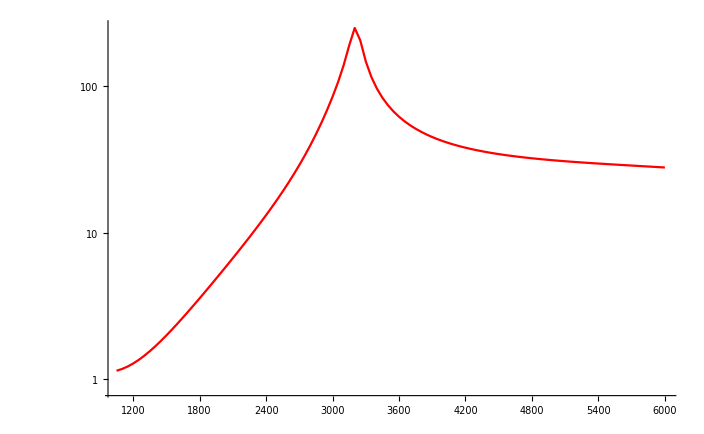

```mathematica
scatteringlength=Table[{masses[[i]],Abs[Sqrt[binding3]masses[[i]]  DARK[masses[[i]],β,δwino,vpot1,vpot5,x0][[3]]]},{i,1,Length[masses]}];
ListLogPlot[scatteringlength,Joined->True,PlotStyle->Red]
```

## wave-functions

```mathematica
β=0.001;
δwino= .166;
x0=1;
eqB[B_,V0_,x0_]:=Abs[√B+√(V0-B) Cot[ √(V0-B)/x0]];
b1=0.1;
b3=b1/2;
b5=b3/9;
vpot1= v0/.FindRoot[eqB[b1,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot3=v0/.FindRoot[eqB[b3,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
vpot5=v0/.FindRoot[eqB[b5,v0,x0]==0,{v0,π^2/4 x0^2}]//Chop
```

3.16113

2.94499

2.6198

2400

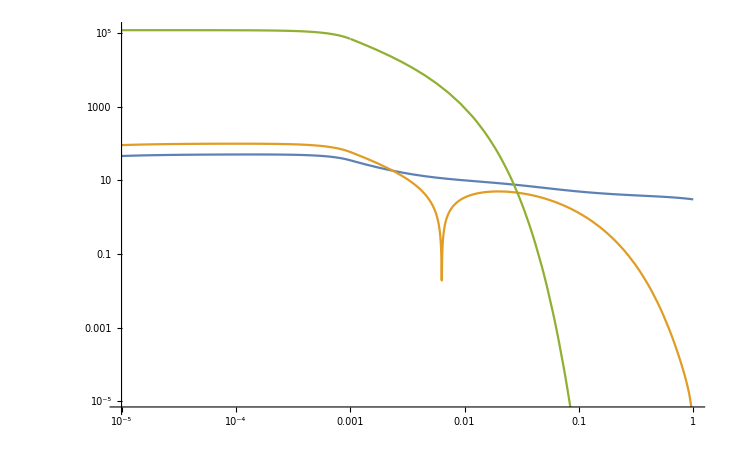

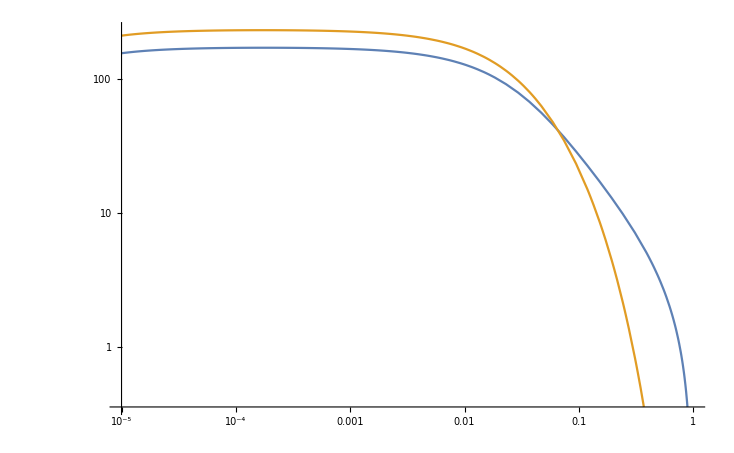

```mathematica
mdm=2400
ψ00tot=mdm β/z DARK[mdm,β,δwino,vpot1,vpot3,vpot5,x0,b3][[1]][z];
ψ10tot=mdm β/z DARK[mdm,β,δwino,vpot1,vpot3,vpot5,x0,b3][[2]][z];
ψ00su2=mdm β/z WINO[mdm,β,δwino][[1]][z];
ψ10su2=mdm β/z WINO[mdm,β,δwino][[2]][z];
chibound[r_,v0_,B_,r0_,M_]:=(√(2 √(M B)))/(√(1+r0 Sqrt[M B]))( Sin[√(M (v0-B))r]UnitStep[r0-r]+ ⅇ^(√(B M) r0) Sin[r0 √(M (-B+v0))] Exp[-√(M B)r]UnitStep[r-r0]);
ψbs=mdm β/z chibound[z/(mdm β),vpot3 mdm,b3 mdm,1/(x0 mdm),mdm];
LogLogPlot[{Abs[ψ00tot],Abs[ψ10tot],ψbs},{z,0.01β/x0,1}]
LogLogPlot[{Abs[ψ00su2],Abs[ψ10su2]},{z,0.01β/x0,1}]
```